```mathematica
(*PROBLEMA 6  INTERFERENCIAS*)
```

```mathematica
(*ÁLVARO MARTÍNEZ Y ANNA IRANZO, GRUPO BU2*)
```

```mathematica
n1=1;
```

```mathematica
n2=1.52;
```

```mathematica
λ0=550*10^(-9);
```

```mathematica
E0=1;
```

```mathematica
(*ζ = k0z*)
```

```mathematica
ζ1=-4*Pi;
```

```mathematica
ζ2=-ζ1;
```

```mathematica
(*APARTADOS A Y B*)
```

```mathematica
nA[ζ_]:=n1*HeavisideTheta[-ζ]+n2*HeavisideTheta[ζ];
```

```mathematica
solA=NDSolve[{e''[ζ]+(nA[ζ])^2*e[ζ]==0,I*n1*e[ζ1]+e'[ζ1]-2*I*n1*E0*Exp[I*nA[ζ1]*ζ1]==0,I*nA[ζ2]*e[ζ2]-e'[ζ2]==0},e,{ζ,ζ1,ζ2}]
```

NDSolve::berr: The scaled boundary value residual error of 1.78165 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{e→InterpolatingFunction[…]}}

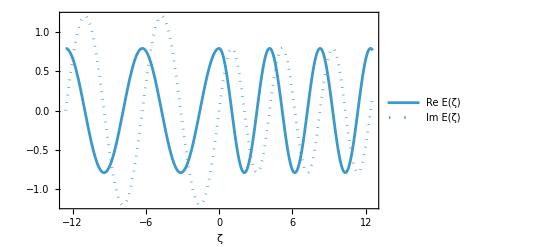

```mathematica
ReImPlot[Evaluate[e[ζ]/.solA],{ζ,ζ1,ζ2},PlotLegends->Automatic,ReImLabels->{"Re E(ζ)", "Im E(ζ)"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]]
```

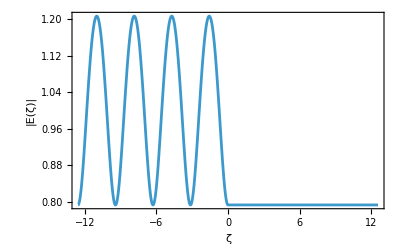

```mathematica
Plot[Abs[Evaluate[e[ζ]/.solA]],{ζ,ζ1,ζ2},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["|E(ζ)|",16,Bold]}]
```

```mathematica
(*APARTADO C*)
```

```mathematica
rAnum=((Evaluate[e[0]/.solA])/E0)-1
```

{-0.206349-1.5609×10^-7 ⅈ}

```mathematica
RAnum=Abs[rAnum]^2
```

{0.0425799}

```mathematica
RAteo=Abs[(n2-n1)/(n2+n1)]^2
```

0.04258

```mathematica
(*APARTADO D*)
```

```mathematica
n1/n2
```

0.657895

```mathematica
nL1=1.38;
```

```mathematica
nL2=1.69;
```

```mathematica
(nL1/nL2)^2
```

0.666783

```mathematica
(*APARTADO E*)
```

```mathematica
dL1=99.6*10^(-9);
```

```mathematica
dL2=81.4*10^(-9);
```

```mathematica
ζL1=(2*Pi/λ0)*dL1;
```

```mathematica
ζL2=(2*Pi/λ0)*dL2;
ζLE=(ζL1+ζL2)+ζ2;
```

```mathematica
nE[ζ_]:=n1*HeavisideTheta[-ζ]+nL1*HeavisideTheta[ζ]+(nL2-nL1)*HeavisideTheta[ζ-ζL1]+(n2-nL2)*HeavisideTheta[ζ-(ζL1+ζL2)];
```

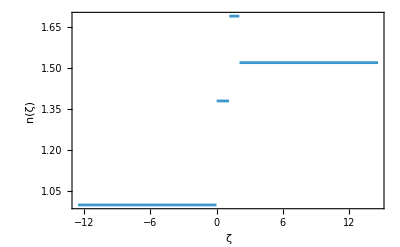

```mathematica
Plot[nE[ζ],{ζ,ζ1,ζLE},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["n(ζ)",16,Bold]}]
```

```mathematica
nE[ζLE]
```

1.52

```mathematica
solE=NDSolve[{e''[ζ]+(nE[ζ])^2*e[ζ]==0,I*n1*e[ζ1]+e'[ζ1]-2*I*n1*E0*Exp[I*nE[ζ1]*ζ1]==0,I*nE[ζLE]*e[ζLE]-e'[ζLE]==0},e,{ζ,ζ1,ζLE}]
```

NDSolve::berr: The scaled boundary value residual error of 1.70179 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{e→InterpolatingFunction[…]}}

```mathematica
(*ReImPlot[Evaluate[e[ζ]/.solE],{ζ,ζ1,ζLE},PlotLegends->Automatic,ReImLabels->{"Re E(ζ)", "Im E(ζ)"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]]*)
```

```mathematica
plotn1=ReImPlot[Evaluate[e[ζ]/.solE],{ζ,ζ1,0},PlotLegends->Automatic,ReImLabels->{"Re E(ζ)", "Im E(ζ)"},PlotRange->{{ζ1,ζLE},Automatic},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
```

```mathematica
plotn2=ReImPlot[Evaluate[e[ζ]/.solE],{ζ,ζL1+ζL2,ζLE},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
```

```mathematica
plotnL=ReImPlot[Evaluate[e[ζ]/.solE],{ζ,0,ζL1+ζL2},PlotLegends->Automatic,ReImLabels->{"Re E(ζ) interfase", "Im E(ζ) interfase"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold],PlotStyle->{Blend[{Red,White}],Thick}];
```

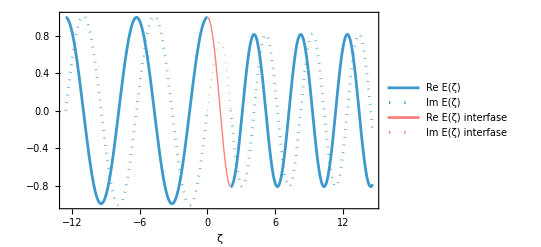

```mathematica
Show[plotn1,plotnL,plotn2]
```

```mathematica
(*Plot[Abs[Evaluate[e[ζ]/.solE]],{ζ,ζ1,ζ2},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["|E(ζ)|",16,Bold]}]*)
```

```mathematica
plotn1Abs=Plot[Abs[Evaluate[e[ζ]/.solE]],{ζ,ζ1,0},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["|E(ζ)|",16,Bold]},PlotRange->{{ζ1,ζLE},{0.7,1.05}},PlotLegends->{"|E(ζ)|"}];
```

```mathematica
plotn2Abs=Plot[Abs[Evaluate[e[ζ]/.solE]],{ζ,ζL1+ζL2,ζLE},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic}];
```

```mathematica
plotnLAbs=Plot[Abs[Evaluate[e[ζ]/.solE]],{ζ,0,ζL1+ζL2},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic},PlotStyle->{Blend[{Red,White}],Thick},PlotLegends->{"|E(ζ)| interfase"}];
```

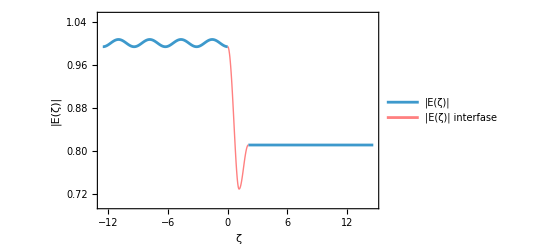

```mathematica
Show[plotn1Abs,plotn2Abs,plotnLAbs]
```

```mathematica
rEnum=((Evaluate[e[0]/.solE])/E0)-1
```

{-0.00670984-0.000106414 ⅈ}

```mathematica
REnum=Abs[rEnum]^2
```

{0.0000450333}

```mathematica
(*APARTADO G*)
ζLG[Ncel_]:=Ncel*(ζL1+ζL2)+ζ2;
```

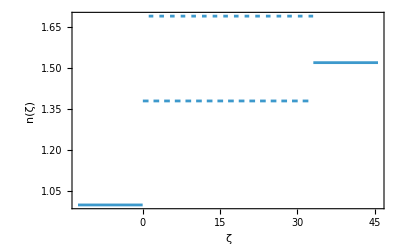

```mathematica
ζNL[Ncel_]:=Ncel*(ζL1+ζL2);
(*Para dos celdas*)nG[ζ_,Ncel_]:=n1*HeavisideTheta[-ζ]+nL1*HeavisideTheta[ζ]+(nL2-nL1)*HeavisideTheta[ζ-ζL1]+(nL1-nL2)*HeavisideTheta[ζ-(ζL1+ζL2)]+ (nL2-nL1)*HeavisideTheta[ζ-(Ncel*ζL1+ζL2)]+(n2-nL2)*HeavisideTheta[ζ-Ncel*(ζL1+ζL2)];
(*Intento general*)
nGgen[ζ_,Ncel_]:=n1*HeavisideTheta[-ζ]+nL1*HeavisideTheta[ζ]+(nL1-nL2)*Sum[HeavisideTheta[ζ-n*(ζL1+ζL2)],{n,1,Ncel}]+ (nL2-nL1)*Sum[HeavisideTheta[ζ-(n*ζL1+(n-1)*ζL2)],{n,1,Ncel}]+(n2-nL1)*HeavisideTheta[ζ-Ncel*(ζL1+ζL2)];

Plot[nGgen[ζ,16],{ζ,ζ1,ζLG[16]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["n(ζ)",16,Bold]}]
```

```mathematica
(*Para Ncel=2*)
solG=NDSolve[{e''[ζ]+(nGgen[ζ,2])^2*e[ζ]==0,I*n1*e[ζ1]+e'[ζ1]-2*I*n1*E0*Exp[I*nGgen[ζ1,2]*ζ1]==0,I*nGgen[ζLG[2],2]*e[ζLG[2]]-e'[ζLG[2]]==0},e,{ζ,ζ1,ζLG[2]}]
```

{{e→InterpolatingFunction[…]}}

```mathematica
(*APARTADO H*)
```

```mathematica
plotn1G=ReImPlot[Evaluate[e[ζ]/.solG],{ζ,ζ1,0},PlotLegends->Automatic,ReImLabels->{"Re E(ζ)", "Im E(ζ)"},PlotRange->{{ζ1,ζLG[2]},Automatic},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
```

```mathematica
plotn2G=ReImPlot[Evaluate[e[ζ]/.solG],{ζ,ζNL[2],ζLG[2]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
```

```mathematica
plotnLG=ReImPlot[Evaluate[e[ζ]/.solG],{ζ,0,ζNL[2]},PlotLegends->Automatic,ReImLabels->{"Re E(ζ) interfase", "Im E(ζ) interfase"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold],PlotStyle->{Blend[{Red,White}],Thick}];
```

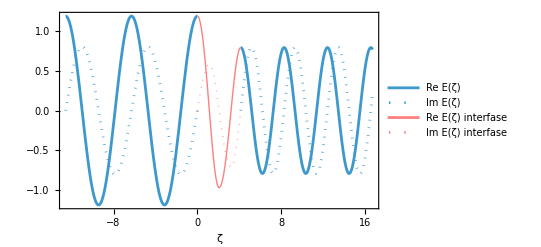

```mathematica
Show[plotn1G,plotnLG,plotn2G]
```

```mathematica
plotn1GAbs=Plot[Abs[Evaluate[e[ζ]/.solG]],{ζ,ζ1,0},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["|E(ζ)|",16,Bold]},PlotRange->{{ζ1,ζLG[2]},{0.55,1.2}},PlotLegends->{"|E(ζ)|"}];
```

```mathematica
plotn2GAbs=Plot[Abs[Evaluate[e[ζ]/.solG]],{ζ,ζNL[2],ζLG[2]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic}];
```

```mathematica
plotnLGAbs=Plot[Abs[Evaluate[e[ζ]/.solG]],{ζ,0,ζNL[2]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic},PlotStyle->{Blend[{Red,White}],Thick},PlotLegends->{"|E(ζ)| interfase"}];
```

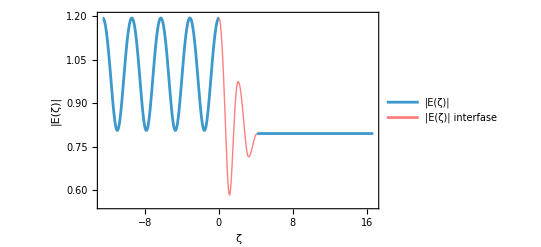

```mathematica
Show[plotn1GAbs,plotn2GAbs,plotnLGAbs]
```

```mathematica
rHnum=((Evaluate[e[0]/.solG])/E0)-1
```

{0.193466-0.000158824 ⅈ}

```mathematica
RHnum=Abs[rHnum]^2
```

{0.037429}

```mathematica
(*APARTADO I*)
(*N=4*)
solI4=NDSolve[{e''[ζ]+(nGgen[ζ,4])^2*e[ζ]==0,I*n1*e[ζ1]+e'[ζ1]-2*I*n1*E0*Exp[I*nGgen[ζ1,4]*ζ1]==0,I*nGgen[ζLG[4],4]*e[ζLG[4]]-e'[ζLG[4]]==0},e,{ζ,ζ1,ζLG[4]}]
```

NDSolve::berr: The scaled boundary value residual error of 3.25557 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{e→InterpolatingFunction[…]}}

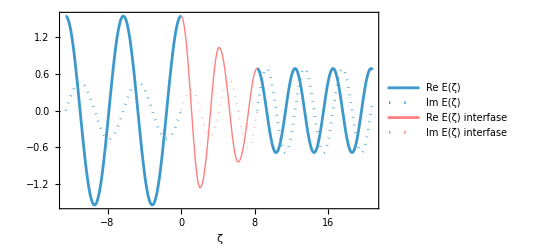

```mathematica
plotn1I4=ReImPlot[Evaluate[e[ζ]/.solI4],{ζ,ζ1,0},PlotLegends->Automatic,ReImLabels->{"Re E(ζ)", "Im E(ζ)"},PlotRange->{{ζ1,ζLG[4]},Automatic},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
plotn2I4=ReImPlot[Evaluate[e[ζ]/.solI4],{ζ,ζNL[4],ζLG[4]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
plotnLI4=ReImPlot[Evaluate[e[ζ]/.solI4],{ζ,0,ζNL[4]},PlotLegends->Automatic,ReImLabels->{"Re E(ζ) interfase", "Im E(ζ) interfase"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold],PlotStyle->{Blend[{Red,White}],Thick}];
Show[plotn1I4,plotnLI4,plotn2I4]
```

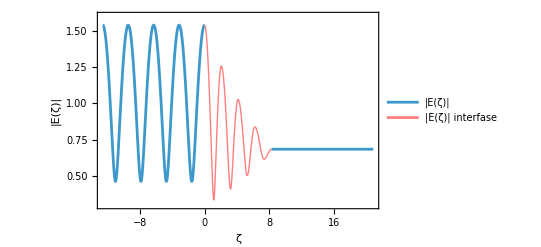

```mathematica
plotn1I4Abs=Plot[Abs[Evaluate[e[ζ]/.solI4]],{ζ,ζ1,0},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["|E(ζ)|",16,Bold]},PlotRange->{{ζ1,ζLG[4]},{0.3,1.6}},PlotLegends->{"|E(ζ)|"}];
plotn2I4Abs=Plot[Abs[Evaluate[e[ζ]/.solI4]],{ζ,ζNL[4],ζLG[4]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic}];
plotnLI4Abs=Plot[Abs[Evaluate[e[ζ]/.solI4]],{ζ,0,ζNL[4]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic},PlotStyle->{Blend[{Red,White}],Thick},PlotLegends->{"|E(ζ)| interfase"}];

Show[plotn1I4Abs,plotn2I4Abs,plotnLI4Abs]
```

```mathematica
rI4num=((Evaluate[e[0]/.solI4])/E0)-1
```

{0.537921-0.000122244 ⅈ}

```mathematica
RI4num=Abs[rI4num]^2
```

{0.289359}

```mathematica
(*N=8*)
```

```mathematica
solI8=NDSolve[{e''[ζ]+(nGgen[ζ,8])^2*e[ζ]==0,I*n1*e[ζ1]+e'[ζ1]-2*I*n1*E0*Exp[I*nGgen[ζ1,8]*ζ1]==0,I*nGgen[ζLG[8],8]*e[ζLG[8]]-e'[ζLG[8]]==0},e,{ζ,ζ1,ζLG[8]}]
```

NDSolve::berr: The scaled boundary value residual error of 4.69464 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{e→InterpolatingFunction[…]}}

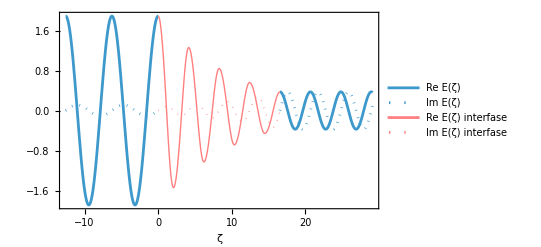

```mathematica
plotn1I8=ReImPlot[Evaluate[e[ζ]/.solI8],{ζ,ζ1,0},PlotLegends->Automatic,ReImLabels->{"Re E(ζ)", "Im E(ζ)"},PlotRange->{{ζ1,ζLG[8]},Automatic},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
plotn2I8=ReImPlot[Evaluate[e[ζ]/.solI8],{ζ,ζNL[8],ζLG[8]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
plotnLI8=ReImPlot[Evaluate[e[ζ]/.solI8],{ζ,0,ζNL[8]},PlotLegends->Automatic,ReImLabels->{"Re E(ζ) interfase", "Im E(ζ) interfase"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold],PlotStyle->{Blend[{Red,White}],Thick}];
Show[plotn1I8,plotnLI8,plotn2I8]
```

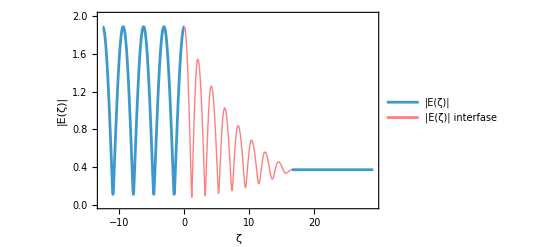

```mathematica
plotn1I8Abs=Plot[Abs[Evaluate[e[ζ]/.solI8]],{ζ,ζ1,0},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["|E(ζ)|",16,Bold]},PlotRange->{{ζ1,ζLG[8]},{0,2}},PlotLegends->{"|E(ζ)|"}];
plotn2I8Abs=Plot[Abs[Evaluate[e[ζ]/.solI8]],{ζ,ζNL[8],ζLG[8]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic}];
plotnLI8Abs=Plot[Abs[Evaluate[e[ζ]/.solI8]],{ζ,0,ζNL[8]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic},PlotStyle->{Blend[{Red,White}],Thick},PlotLegends->{"|E(ζ)| interfase"}];

Show[plotn1I8Abs,plotn2I8Abs,plotnLI8Abs]
```

```mathematica
rI8num=((Evaluate[e[0]/.solI8])/E0)-1
```

{0.887877+0.000078955 ⅈ}

```mathematica
RI8num=Abs[rI8num]^2
```

{0.788326}

```mathematica
(*N=16*)
```

```mathematica
solI16=NDSolve[{e''[ζ]+(nGgen[ζ,16])^2*e[ζ]==0,I*n1*e[ζ1]+e'[ζ1]-2*I*n1*E0*Exp[I*nGgen[ζ1,16]*ζ1]==0,I*nGgen[ζLG[16],16]*e[ζLG[16]]-e'[ζLG[16]]==0},e,{ζ,ζ1,ζLG[16]}]
```

NDSolve::berr: The scaled boundary value residual error of 20.8543 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{e→InterpolatingFunction[…]}}

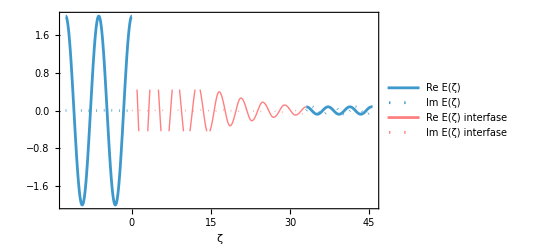

```mathematica
plotn1I16=ReImPlot[Evaluate[e[ζ]/.solI16],{ζ,ζ1,0},PlotLegends->Automatic,ReImLabels->{"Re E(ζ)", "Im E(ζ)"},PlotRange->{{ζ1,ζLG[16]},Automatic},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
plotn2I16=ReImPlot[Evaluate[e[ζ]/.solI16],{ζ,ζNL[16],ζLG[16]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold]];
plotnLI16=ReImPlot[Evaluate[e[ζ]/.solI16],{ζ,0,ζNL[16]},PlotLegends->Automatic,ReImLabels->{"Re E(ζ) interfase", "Im E(ζ) interfase"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->Style[ζ,16,Bold],PlotStyle->{Blend[{Red,White}],Thick}];
Show[plotn1I16,plotnLI16,plotn2I16]
```

```mathematica
plotn1I16Abs=Plot[Abs[Evaluate[e[ζ]/.solI16]],{ζ,ζ1,0},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Style["|E(ζ)|",16,Bold]},PlotRange->{{ζ1,ζLG[16]},{0,2}},PlotLegends->{"|E(ζ)|"}];
plotn2I16Abs=Plot[Abs[Evaluate[e[ζ]/.solI16]],{ζ,ζNL[16],ζLG[16]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic}];
plotnLI16Abs=Plot[Abs[Evaluate[e[ζ]/.solI16]],{ζ,0,ζNL[16]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},Frame->True,FrameLabel->{Style[ζ,16,Bold],Automatic},PlotStyle->{Blend[{Red,White}],Thick},PlotLegends->{"|E(ζ)| interfase"}];

Show[plotn1I8Abs,plotn2I8Abs,plotnLI8Abs]
```

-Graphics-

```mathematica
rI16num=((Evaluate[e[0]/.solI16])/E0)-1
```

{0.99537+0.000174198 ⅈ}

```mathematica
RI16num=Abs[rI16num]^2
```

{0.990761}

```mathematica
(*APARTADO J*)
```

```mathematica
ρ[Ncel_]:=(n1/n2)*(nL2/nL1)^(2*Ncel);
```

```mathematica
R2=((1-ρ[2])/(1+ρ[2]))^2
```

0.0374289

```mathematica
R4=((1-ρ[4])/(1+ρ[4]))^2
```

0.289359

```mathematica
R8=((1-ρ[8])/(1+ρ[8]))^2
```

0.788325

```mathematica
R16=((1-ρ[16])/(1+ρ[16]))^2
```

0.990761